```mathematica
AppendTo[$Path,NotebookDirectory[]<>"../src"];
<<affine.m;
```

```mathematica
b2=Subscript[B, 2];
```

```mathematica
m=makeIrreducibleModule[b2][3,2];
```

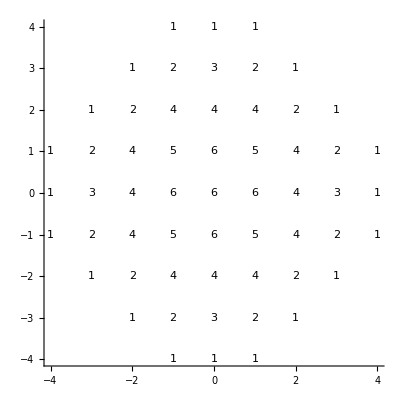

```mathematica
textPlot[m,{Axes->True}]
```

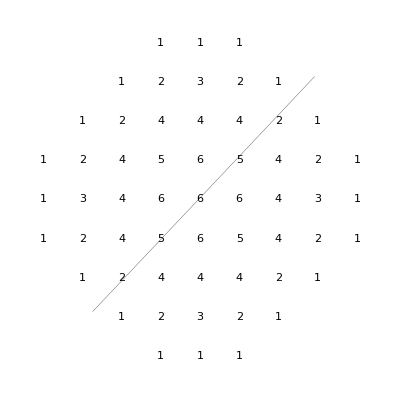

```mathematica
se=singularElement[m];
```

```mathematica
se
```

formalElement[Affine`Private`table$1278]

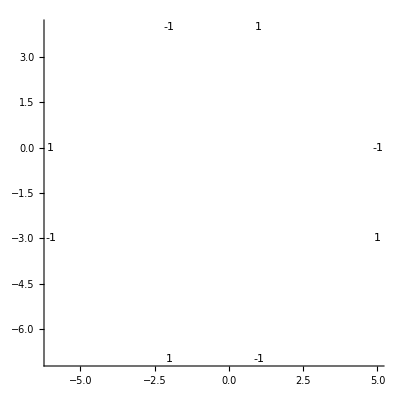

```mathematica
drawPlaneProjection[2,1,se,{Axes->True}]
```

```mathematica
externalContour[axe1_,axe2_,f_formalElement,style_:Dashed,opts___?OptionQ]:=Graphics[
{(Text[f[#],{#[standardBase][[axe1]],#[standardBase][[axe2]]-0.25}])&/@f[weights],
{style,JoinedCurve[Line[Sort[{#[standardBase][[axe1]],#[standardBase][[axe2]]}&/@f[weights], ArcTan@@#1>ArcTan@@#2&]],CurveClosed->True]}},opts]
```

```mathematica
Sort[{#[standardBase][[1]],#[standardBase][[2]]}&/@se[weights], ArcTan@@#1>ArcTan@@#2&]
```

{{-7,-2},{-3,-6},{0,-6},{4,-2},{4,1},{0,5},{-3,5},{-7,1}}

```mathematica
externalContour[axe1_,axe2_,f_formalElement,style_:Dashed,opts___?OptionQ]:=Graphics[
(Text[{f[#],#[standardBase][[axe1]],#[standardBase][[axe2]]}])&/@f[weights]];
```

```mathematica
externalContour[2,1,se,Dotted,Axes->True]
```

-Graphics-

```mathematica
Inverse[Transpose[cartanMatrix[b2]]]
```

{{1,1},{1/2,1}}

```mathematica
splint[al_finiteRootSystem,{rts__?weightQ}]:=(Inverse[Transpose[cartanMatrix[al]]].dynkinLabels[al][#]).{rts}&;
```

```mathematica
splint[Subscript[A, 2],{makeFiniteWeight[{1,0}],makeFiniteWeight[{0,1}]}]@weight[Subscript[A, 2]][1,0]
```

finiteWeight[2,{2/3,1/3}]

```mathematica
se2=singularElement[makeIrreducibleModule[Subscript[A, 2]][3,2]]
```

formalElement[Affine`Private`table$2855]

```mathematica
sp=splint[Subscript[A, 2],{makeFiniteWeight[{1,0}],makeFiniteWeight[{0,1}]}];
```

```mathematica
sp@weight[Subscript[A, 2]][3,2]
```

finiteWeight[2,{8/3,7/3}]

```mathematica
sp/@se2[weights]
```

```mathematica
sp@rho[Subscript[A, 2]]
```

finiteWeight[2,{1,1}]

```mathematica
(Exp[weight[Subscript[B, 2]][1,-1]]*makeFormalElement[sp/@se2[weights],se2[multiplicities]])[weights]
```

{finiteWeight[2,{17/6,13/6}],finiteWeight[2,{-1/6,13/6}],finiteWeight[2,{17/6,-11/6}],finiteWeight[2,{-25/6,-11/6}],finiteWeight[2,{-1/6,-29/6}],finiteWeight[2,{-25/6,-29/6}]}

```mathematica
externalContour[2,1,Exp[3/2*weight[Subscript[B, 2]][2,-2]]*makeFormalElement[sp/@se2[weights],se2[multiplicities]]+Exp[makeFiniteWeight[{-1/6,1/6}]]*Exp[-4/2*weight[Subscript[B, 2]][2,-2]]*makeFormalElement[sp/@se2[weights],se2[multiplicities]],Dashed,Axes->True]
```

-Graphics-

```mathematica
{{2,-2},{-1,2}}
```

```mathematica
externalContour[2,1,singularElement[makeIrreducibleModule[Subscript[B, 2]][0,1]],Dotted,Axes->True]
```

-Graphics-

```mathematica
simpleRoots[b2]
```

{finiteWeight[2,{1,-1}],finiteWeight[2,{0,1}]}

```mathematica
fundamentalWeights[b2]
```

{finiteWeight[2,{1,0}],finiteWeight[2,{1/2,1/2}]}

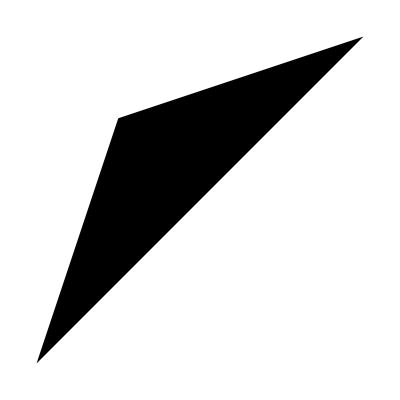

```mathematica
Graphics[Polygon[{{1,1},{2,2},{-1,1},{-2,-2}}]]
```

```mathematica
?Polygon
```

Polygon[{pt_1,pt_2,…}] is a graphics primitive that represents a filled polygon. 
Polygon[{{pt_11,pt_12,…},{pt_21,…},…}] represents a collection of polygons.

```mathematica
?Line
```

Line[{pt_1,pt_2,…}] is a graphics primitive which represents a line joining a sequence of points. 
Line[{{pt_11,pt_12,…},{pt_21,…},…}] represents a collection of lines.